```mathematica
thilo="d:\\Users\\Johannes\\Desktop\\diplom\\mat_backup\\nucleon3pt.790.m0.200.a0";pos="d:\\Users\\Johannes\\Projekte\\Diplom\\results_backup_cluster\\pos.pol.24\\nucleon3pt.790.m0.200.a0";
```

```mathematica
neg="d:\\Users\\Johannes\\Projekte\\Diplom\\results_backup_cluster\\neg.pol.10\\nucleon3pt.790.m0.200.a0";
avg="d:\\Users\\Johannes\\Projekte\\Diplom\\results_backup_cluster\\average\\a0\\200";
```

```mathematica
c3=(#[[2]]+I#[[3]])&/@Import[pos, "Table"] ;c2=(#[[2]]+I#[[3]])&/@Import["d:\\Users\\Johannes\\Projekte\\Diplom\\results_backup_cluster\\pos.pol.24\\200", "Table" ];
c2n=(#[[2]]+I#[[3]])&/@Import["d:\\Users\\Johannes\\Projekte\\Diplom\\results_backup_cluster\\neg.pol.10\\200", "Table" ];
tc3=(#[[2]]+I#[[3]])&/@Import[thilo, "Table"] ;
```

```mathematica
mc2=Table[{Mean[Re[Log[#]]],StandardDeviation[Re[Log[#]]]}&[Table[c2[[j+i*32]],{i,0,99}]],{j,2,32}];
ten=Table[Table[c2n[[j+i*32]],{i,0,99}],{j,1,32}];
te=Table[Table[c2[[j+i*32]],{i,0,99}],{j,1,32}];
mc2n=Table[{Re[Mean[#]],Re[StandardDeviation[#]],j}&[Table[c2n[[j+i*32]],{i,0,99}]],{j,32,1,-1}];
mc3=Table[Sum[c3[[j+i*32]],{i,0,99}],{j,32}];
mtc3=Table[Sum[tc3[[j+i*32]],{i,0,99}],{j,32}];
```

127877.

2.18532

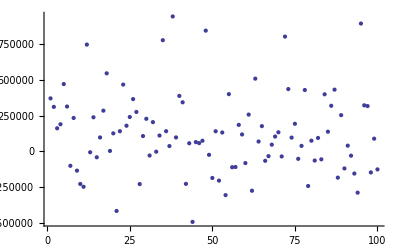

```mathematica
Mean[Re[-te[[24]]]]
StandardDeviation[Re[-te[[24]]]]/Mean[Re[-te[[24]]]]
ListPlot[Re[-te[[24]]]]
```

121434.

2.15014

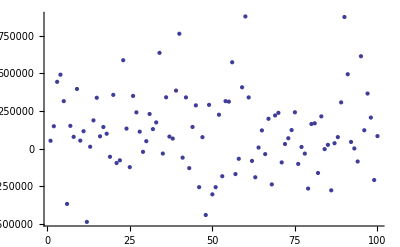

```mathematica
Mean[Re[ten[[10]]]]
StandardDeviation[Re[ten[[10]]]]/Mean[Re[ten[[10]]]]
ListPlot[Re[ten[[10]]]]
```

```mathematica
mc2n[[1]]
```

-1.0805×10^15-1.91479×10^11 ⅈ

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ErrorListPlot[{{1,ErrorBar[{1,2}]}}, AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
mc2n
```

{{2.00638×10^12,3.26645×10^11,32},{4.27819×10^11,8.61311×10^10,31},{9.79242×10^10,2.3766×10^10,30},{2.27944×10^10,6.7365×10^9,29},{5.34008×10^9,1.8437×10^9,28},{1.27618×10^9,5.23601×10^8,27},{3.07989×10^8,1.45842×10^8,26},{7.45437×10^7,3.90315×10^7,25},{1.77805×10^7,1.01022×10^7,24},{4.24884×10^6,2.67017×10^6,23},{1.00317×10^6,693449.,22},{235530.,174839.,21},{55494.1,44888.1,20},{12894.4,11867.3,19},{2947.1,3281.86,18},{668.202,989.69,17},{141.466,700.902,16},{1.46911,1112.8,15},{-94.5661,2332.57,14},{-188.539,7289.72,13},{531.458,26678.7,12},{12594.,93939.2,11},{121434.,350461.,10},{851365.,1.37881×10^6,9},{4.88989×10^6,5.84092×10^6,8},{2.82246×10^7,2.51239×10^7,7},{1.69104×10^8,1.09398×10^8,6},{9.93808×10^8,4.99572×10^8,5},{5.72738×10^9,2.32142×10^9,4},{5.01073×10^10,1.44545×10^10,3},{4.24581×10^11,8.5518×10^10,2},{-1.0805×10^13,1.46724×10^12,1}}

```mathematica
a={{#[[3]],Log[#[[1]]]},ErrorBar[{Log[1+#[[2]]/#[[1]]],Log[1-#[[2]]/#[[1]]]}]}&/@mc2n
```

{{{32,28.3274},ErrorBar[{0.150833,-0.177696}]},{{31,26.782},ErrorBar[{0.183426,-0.224802}]},{{30,25.3075},ErrorBar[{0.217285,-0.277994}]},{{29,23.8498},ErrorBar[{0.258923,-0.350314}]},{{28,22.3985},ErrorBar[{0.296585,-0.423513}]},{{27,20.9671},ErrorBar[{0.343793,-0.528119}]},{{26,19.5456},ErrorBar[{0.387662,-0.641563}]},{{25,18.1269},ErrorBar[{0.42108,-0.74151}]},{{24,16.6936},ErrorBar[{0.449903,-0.839702}]},{{23,15.2622},ErrorBar[{0.487626,-0.990061}]},{{22,13.8187},ErrorBar[{0.525472,-1.17524}]},{{21,12.3696},ErrorBar[{0.555219,-1.35605}]},{{20,10.924},ErrorBar[{0.592709,-1.65486}]},{{19,9.46455},ErrorBar[{0.652505,-2.53005}]},{{18,7.98858},ErrorBar[{0.748387,-2.17517+3.14159 ⅈ}]},{{17,6.50459},ErrorBar[{0.908711,-0.731631+3.14159 ⅈ}]},{{16,4.95206},ErrorBar[{1.78416,1.37487+3.14159 ⅈ}]},{{15,0.384658},ErrorBar[{6.6313,6.62866+3.14159 ⅈ}]},{{14,4.5493+3.14159 ⅈ},ErrorBar[{3.16404+3.14159 ⅈ,3.24517}]},{{13,5.23931+3.14159 ⅈ},ErrorBar[{3.62871+3.14159 ⅈ,3.68045}]},{{12,6.27562},ErrorBar[{3.93572,3.89588+3.14159 ⅈ}]},{{11,9.44097},ErrorBar[{2.13524,1.86549+3.14159 ⅈ}]},{{10,11.7071},ErrorBar[{1.35739,0.634471+3.14159 ⅈ}]},{{9,13.6546},ErrorBar[{0.962994,-0.478796+3.14159 ⅈ}]},{{8,15.4027},ErrorBar[{0.785949,-1.63738+3.14159 ⅈ}]},{{7,17.1557},ErrorBar[{0.636651,-2.20855}]},{{6,18.946},ErrorBar[{0.498909,-1.04107}]},{{5,20.7171},ErrorBar[{0.407253,-0.698531}]},{{4,22.4685},ErrorBar[{0.340265,-0.519732}]},{{3,24.6374},ErrorBar[{0.253456,-0.34034}]},{{2,26.7744},ErrorBar[{0.183502,-0.224917}]},{{1,30.011+3.14159 ⅈ},ErrorBar[{-0.145943,0.127331}]}}

```mathematica
Pi//N
```

3.14159

```mathematica
a[[14]]
```

{{19,9.46455},ErrorBar[{2.53005,-0.652505}]}

```mathematica
ErrorListPlot[a]
```

-Graphics-

```mathematica
mc2n[[1]]
```

-1.08043×10^15-3.43494×10^11 ⅈ

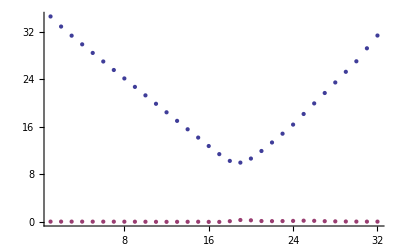

```mathematica
ListPlot[{Re[Log[-mc2]],Im[Log[-mc2]]}]
```

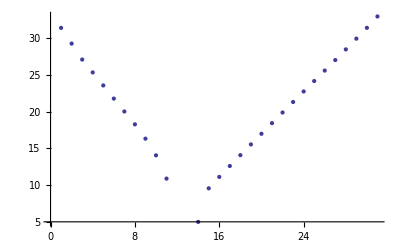

```mathematica
ListPlot[{Log[Re[te]]}]
```

```mathematica
mc2[[24]]
```

-1.27877×10^7-1.51982×10^6 ⅈ

```mathematica
mc2n[[23]]
```

1.21434×10^7+305622. ⅈ

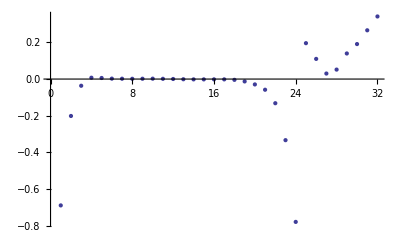

```mathematica
ListPlot[{Im[mc3]/Re[mc2n[[23]]]},PlotRange->Full]
```

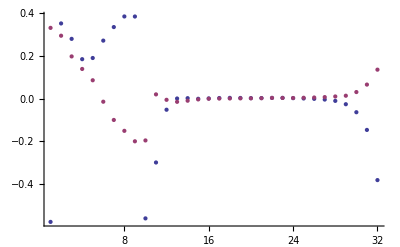

```mathematica
ListPlot[{Im[mc3]/Re[mc2[[24]]],Re[mc3]/Re[mc2[[24]]]}]
```

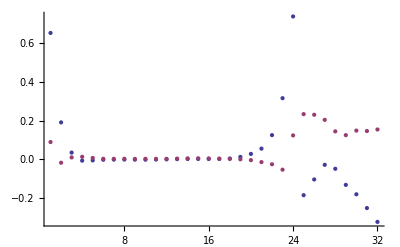

```mathematica
ListPlot[{Im[mc3]/Re[mc2[[24]]],Re[mc3]/Re[mc2[[24]]]}]
```

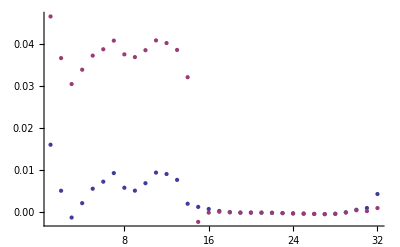

```mathematica
ListPlot[{Re[mtc3/mc2[[14]]],Re[mtc3]/Re[mc2[[14]]]}]
```

```mathematica
{{1,2,3}}/{{10,100,1000}}
```

{{1/10,1/50,3/1000}}

```mathematica
Log[-4]
```

ⅈ π+Log[4]

```mathematica
Sin[#]&/@{1,2,3}
```

{Sin[1],Sin[2],Sin[3]}